Created by: jacobm on 12-19-2017 20:20:21

### Categorization

Symbol

Synonyms

### Keywords

### Syntax Templates

Details

Security Details

"   Potential security risk"

# QuantumDiscreteState

QuantumDiscreteState[{qob_1 → vals_1, qob_2 → vals_2}] 
yields the discrete quantum state in which quantum objects qob_i assume values vals_i.
      QuantumDiscreteState[{{qob_1, qob_2, …} → vals}]
yields the discrete quantum state in which potentially entangled quantum objects qob_i assume values vals.
      QuantumDiscreteState[{"Product"→{qstate_1, qstate_2, …}}]
yields the quantum state formed by taking the tensor product of discrete quantum states qstate_i.
      QuantumDiscreteState[{"Mixture"→ <|{qstate_1→ prob_1, qstate_2→ prob_2, …}|>}]
yields the mixed quantum state formed from a statistical ensemble in which qstate_i has weight prob_i.
      QuantumDiscreteState[{"Trace"→ {qstate,{qob_1, qob_2, …}}}]
yields the quantum discrete state resulting from tracing out subsystems qob_i from qstate.

## Tutorials

Related Demonstrations

## Related Links

## See Also

## More About

Autogenerated

## Examples | More Examples ⊳

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a two-level quantum system, or "qubit", in the "0" computational basis state:

```mathematica
QuantumDiscreteState[{"wire1" -> {"BasisState", {0}}}]
```

QuantumDiscreteState[…]

View the qubit on the Bloch Sphere:

```mathematica
%["BlochPlot"]
```

-Graphics3D-

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Initialize a 3-qubit register in the "4" number state:

```mathematica
reg = QuantumDiscreteState[{{"w1", "w2", "w3"} -> {"Register", 4}}]
```

QuantumDiscreteState[…]

```mathematica
reg["StateVector"]//MatrixForm
```

(0
0
0
0
1
0
0
0)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a random pure state for a five-level quantum system:

```mathematica
s = QuantumDiscreteState[{"w1" -> "RandomPure"}, "QuditDimension" -> 5]
```

QuantumDiscreteState[…]

Plot its amplitudes and relative phases:

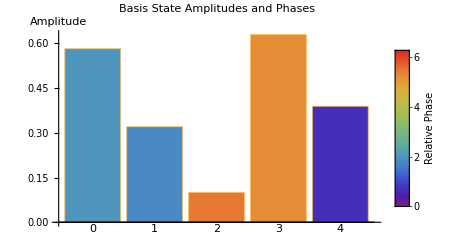

```mathematica
s["Plot"]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate a product state of two three level quantum systems:

```mathematica
qstate = QuantumDiscreteState[{"a" -> {1,0, 0}, "b" -> {1/Sqrt[2],0,1/Sqrt[2]}}, "QuditDimension" -> 3]
```

QuantumDiscreteState[…]

View its state vector:

```mathematica
%["StateVector"]//Normal//MatrixForm
```

(1/(√2)
0
1/(√2)
0
0
0
0
0
0)

Trace out object "a"

```mathematica
reducedState = QuantumDiscreteState[{"Trace" ->  {qstate, "a"}}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a Bell state for two qubits:

```mathematica
bell = QuantumDiscreteState[{{"w1", "w2"} -> "PhiPlus"}]
```

QuantumDiscreteState[…]

Verify the two subsystems are entangled:

```mathematica
QuantumEntangledObjectsQ[bell, {"w1", "w2"}]
```

True

Query for the ordering of basis states in the state vector:

```mathematica
bell["BasisStates"]
```

{00,01,10,11}

```mathematica
bell["BasisLabels"]
```

w1,w2

## More Examples

### Scope

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Specify the dimension of the quantum system:

```mathematica
QuantumDiscreteState[{"w1" -> "PureUniformSuperposition"}, "QuditDimension" -> 4]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Specify combined basis states:

```mathematica
qstate = QuantumDiscreteState[{{"w1", "w2", "w3"} -> {"BasisState", {1, 0,1}}}]
```

QuantumDiscreteState[…]

```mathematica
qstate["StateVector"]//MatrixForm
```

(0
0
0
0
0
1
0
0)

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Numerically specified quantum states are automatically normalized:

```mathematica
QuantumDiscreteState[{{"q"} -> {1,2}}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Quantum states can also be created with keyword "QuantumObjects":

```mathematica
QuantumDiscreteState[{"QuantumObjects" -> {"q" -> "Plus"}}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Entangled states may be input using nested arrays, listing components in the combined basis:

```mathematica
QuantumDiscreteState[{{"w1", "w2"} -> {{α,β},{γ, δ}}}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Mixed states can be specified by density matrices:

```mathematica
QuantumDiscreteState[{"w" -> {{1/2,0},{0, 1/2}}}]
```

QuantumDiscreteState[…]

```mathematica
%["MixedStateQ"]
```

True

### Generalizations & Extensions

### Options

### Applications

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate qubits in basis states of alternative bases:

```mathematica
left = QuantumDiscreteState[{"w" -> "Left"}]
```

QuantumDiscreteState[…]

```mathematica
right = QuantumDiscreteState[{"w" -> "Right"}]
```

QuantumDiscreteState[…]

```mathematica
plus = QuantumDiscreteState[{"w" -> "Plus"}]
```

QuantumDiscreteState[…]

```mathematica
minus = QuantumDiscreteState[{"w" -> "Minus"}]
```

QuantumDiscreteState[…]

Plot all four on the Bloch Sphere:

```mathematica
QuantumBlochPlot[{left -> Red, right -> Yellow, plus -> Green, minus -> Blue}]
```

-Graphics3D-

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Generate all four Bell states:

```mathematica
phiP = QuantumDiscreteState[{{"w1", "w2"} -> "PhiPlus"}]
```

QuantumDiscreteState[…]

```mathematica
phiM = QuantumDiscreteState[{{"w1", "w2"} -> "PhiMinus"}]
```

QuantumDiscreteState[…]

```mathematica
psiP = QuantumDiscreteState[{{"w1", "w2"} -> "PsiPlus"}]
```

QuantumDiscreteState[…]

```mathematica
psiM = QuantumDiscreteState[{{"w1", "w2"} -> "PsiMinus"}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a four-qubit W-state

```mathematica
w = QuantumDiscreteState[{{1,2,3,4} -> "W"}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a three-qubit GHZ state:

```mathematica
ghz = QuantumDiscreteState[{{"w1", "w2", "w3"} -> "GHZ"}]
```

QuantumDiscreteState[…]

Plot its amplitudes:

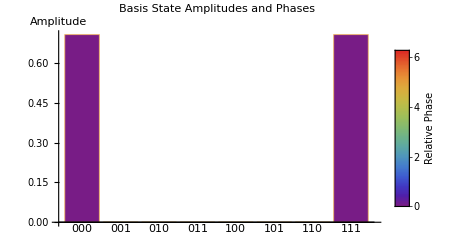

```mathematica
ghz["Plot"]
```

Tracing out subsystems of a pure state can result in a mixed state

```mathematica
sReduced = QuantumDiscreteState[{"Trace"->  {ghz, {"w1", "w2"}}}]
```

QuantumDiscreteState[…]

```mathematica
sReduced["Purity"]
```

1/2

This is a maximally mixed state:

```mathematica
sReduced["BlochSphericalCoordinates"]
```

{r→0,θ→0,ϕ→0}

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a product state from two existing states:

```mathematica
s1 = QuantumDiscreteState[{"w1" -> {1,ⅈ}}]
```

QuantumDiscreteState[…]

```mathematica
s2 =  QuantumDiscreteState[{"w2" -> {-1,ⅈ}}]
```

QuantumDiscreteState[…]

```mathematica
sProd = QuantumDiscreteState[{"Product" ->  {s1, s2}}]
```

QuantumDiscreteState[…]

Perform a partial trace operation to discard system "w2":

```mathematica
sReduced = QuantumDiscreteState[{"Trace"-> {sProd, "w2"}}]
```

QuantumDiscreteState[…]

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]];
```

Create a classical ensemble of quantum states:

```mathematica
s1 = QuantumDiscreteState[{"w" -> {1,.2}}]
```

QuantumDiscreteState[…]

```mathematica
s2 =  QuantumDiscreteState[{"w" -> {-1,3ⅈ}}]
```

QuantumDiscreteState[…]

```mathematica
sMix = QuantumDiscreteState[{"Mixture"->  <|{s1 -> .3, s2 -> .7}|>}]
```

QuantumDiscreteState[…]

Visualize the density matrix

```mathematica
sMix["DensityMatrix"]//Normal//MatrixForm
```

(0.358462+0. ⅈ | 0.0576923-0.21 ⅈ
0.0576923+0.21 ⅈ | 0.641538+0. ⅈ)

```mathematica
sMix["Plot"]
```

-Graphics3D-

Plot the mixed state on the Bloch sphere:

```mathematica
sMix["BlochPlot"]
```

-Graphics3D-

Obtain its purity and Von Neumann Entropy:

```mathematica
sMix["Purity"]
```

0.634923

```mathematica
sMix["VonNeumannEntropy"]
```

0.795483

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

Design Discussion

Application Notes

Test Cases

Function Essay